#### Preamble

```mathematica
ClearAll@@{$Context<>"*"}
SetDirectory[NotebookDirectory[]]
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; 
StartScheduledTask[saveTask] (*Saves nb each 15 minutes*) ;

<<"MaTeX`"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Maxima_Minima.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optics_Mie.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/jet_jet-extended.wls"
```

/home/juanathan/Documentos/MSc_Thesis/3-FEM-Calc/2-Supported-TotallyEmbbeded

#### Plots format

```mathematica
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
colors[[1]] = ColorData[3,2];
PrependTo[colors,Black];
```

```mathematica
fs=9;
cdata3 = Table[ColorData[3,i],{i,10}];cdata3[[3]] = Purple;
texStyle:={FontFamily->"Latin Modern Roman",FontSize->fs,Black};
```

```mathematica
graphsOpts:={Mesh->Full,BaseStyle->texStyle,Frame->True,FrameStyle->Black,ImageSize->215,PlotStyle->colors}
graphsOptsDash:={Mesh->Full,BaseStyle->texStyle,Frame->True,FrameStyle->Black,ImageSize->215,PlotStyle->Table[Directive[Dashed,colors[[i]]],{i,10}]}
```

```mathematica
graphsOptsPolar:={Mesh->30,BaseStyle->texStyle,PolarAxes->True,FrameStyle->Black,ImageSize->215,
	PlotStyle->Table[Directive[PointSize[.015],colors[[i]]],{i,10}],PolarGridLines->Automatic,Joined->True,GridLinesStyle->Directive[Gray,Opacity[.1]],
	PolarAxesOrigin->{{Left,Up},Automatic}}
graphsOptsPolarDashed:={Mesh->30,BaseStyle->texStyle,PolarAxes->True,FrameStyle->Black,ImageSize->215,
	PlotStyle->Table[Directive[Dashed,PointSize[.015],colors[[i]]],{i,10}],PolarGridLines->Automatic,Joined->True,GridLinesStyle->Directive[Gray,Opacity[.1]],
	PolarAxesOrigin->{{Left,Up},Automatic}}
```

```mathematica
graphsOptsDensity := { BaseStyle -> texStyle, FrameStyle -> Black, PlotRange -> Full,  ColorFunctionScaling -> True, ColorFunction -> JetExtended, Mesh -> None, ImageSize -> 150, PlotRangePadding -> None  }
```

#### Sorting Functions

```mathematica
maxPair[list_,ind_]:= SortBy[list, #[[ind]]&][[-1,{1,ind}]]
makePairs[list_,ind_]:=Map[Table[#[[;;,{1,i}]],{i,ind}]&,list]
```

Efficiencies

### Mie

```mathematica
radius = 12.5;
nNP=JohnsonChristyAuRefSize[#,radius]&;
wlength=Range[400,600,2.5];
max=scaQ=extQ={0,0};

scaFunc[lda_]:=Map[MieScatteringQ[{nMat[#],nNP[#]},#,radius]&,toMap[lda]];
extFunc[lda_]:=Map[MieExtinctionQ[{nMat[#],nNP[#]},#,radius]&,toMap[lda]];
```

```mathematica
i=1;
nMat=1.&;
extQ[[i]]=extFunc[wlength];
scaQ[[i]]=scaFunc[wlength];
max[[i]]=FindExtrema[#,wlength[[{1,-1}]],10.,"Maxima"][[1,1]]&/@{extFunc,scaFunc};

i++;
nMat=1.5&;
extQ[[i]]=extFunc[wlength];
scaQ[[i]]=scaFunc[wlength];
max[[i]]=FindExtrema[#,wlength[[{10,-1}]],10.,"Maxima"][[1,1]]&/@{extFunc,scaFunc};

max=Reverse@Transpose[max];
```

```mathematica
mie=MapThread[Show[{ListLogPlot[#,DataRange->wlength[[{1,-1}]],Joined->True,PlotStyle->{Directive[Thick,Dashed,Green],Directive[Thick,Dashed,Magenta]}],
ListLogPlot[Callout[#,ToString[IntegerPart@#[[1]]],Left]&/@#2]},PlotRange->All]&,{{scaQ,extQ-scaQ},max}]
```

{-Graphics-,-Graphics-}

### Interface

```mathematica
data = FileNames["1*","Oblique*"]; data//TableForm
data =Drop[Import[#,"Data"],5]&/@ data;
data[[2]]
cases = {2,3,5,6,8,9,11,12};
data = makePairs[data,cases];
data[[2]]
```

Oblique-Supported-Internal/1-Efficiency-p.csv
Oblique-Supported-Internal/1-Efficiency-s.csv

{{400,0.00669546,0.468191,0.474887,0.00669546,0.468191,0.474887,0.00669546,0.468191,0.474887,0.00669546,0.468191,0.474887},{410,0.00611867,0.456277,0.462396,0.00611867,0.456277,0.462396,0.00611867,0.456277,0.462396,0.00611867,0.456277,0.462396},{420.,0.00559701,0.444786,0.450383,0.00559701,0.444786,0.450383,0.00559701,0.444786,0.450383,0.00559701,0.444786,0.450383},{430.,0.0050718,0.435365,0.440437,0.0050718,0.435365,0.440437,0.0050718,0.435365,0.440437,0.0050718,0.435365,0.440437},{440.,0.00468881,0.434065,0.438754,0.00468881,0.434065,0.438754,0.00468881,0.434065,0.438754,0.00468881,0.434065,0.438754},{450,0.00438003,0.437639,0.442019,0.00438003,0.437639,0.442019,0.00438003,0.437639,0.442019,0.00438003,0.437639,0.442019},{460,0.0040375,0.439917,0.443955,0.0040375,0.439917,0.443955,0.0040375,0.439917,0.443955,0.0040375,0.439917,0.443955},{470,0.00374462,0.445258,0.449003,0.00374462,0.445258,0.449003,0.00374462,0.445258,0.449003,0.00374462,0.445258,0.449003},{480,0.00358265,0.462605,0.466188,0.00358265,0.462605,0.466188,0.00358265,0.462605,0.466188,0.00358265,0.462605,0.466188},{490,0.00362004,0.497485,0.501105,0.00362004,0.497485,0.501105,0.00362004,0.497485,0.501105,0.00362004,0.497485,0.501105},{500,0.00405837,0.547196,0.551254,0.00405837,0.547196,0.551254,0.00405837,0.547196,0.551254,0.00405837,0.547196,0.551254},{502.5,0.00424378,0.559488,0.563732,0.00424378,0.559488,0.563732,0.00424378,0.559488,0.563732,0.00424378,0.559488,0.563732},{505,0.0043899,0.570225,0.574615,0.0043899,0.570225,0.574615,0.0043899,0.570225,0.574615,0.0043899,0.570225,0.574615},{507.5,0.00464189,0.578149,0.58279,0.00464189,0.578149,0.58279,0.00464189,0.578149,0.58279,0.00464189,0.578149,0.58279},{510.,0.0048281,0.582687,0.587515,0.0048281,0.582687,0.587515,0.0048281,0.582687,0.587515,0.0048281,0.582687,0.587515},{512.5,0.00501294,0.58197,0.586983,0.00501294,0.58197,0.586983,0.00501294,0.58197,0.586983,0.00501294,0.58197,0.586983},{515,0.00525862,0.5756,0.580859,0.00525862,0.5756,0.580859,0.00525862,0.5756,0.580859,0.00525862,0.5756,0.580859},{517.5,0.00541194,0.563404,0.568816,0.00541194,0.563404,0.568816,0.00541194,0.563404,0.568816,0.00541194,0.563404,0.568816},{520.,0.0055126,0.546199,0.551712,0.0055126,0.546199,0.551712,0.0055126,0.546199,0.551712,0.0055126,0.546199,0.551712},{522.5,0.00555428,0.524098,0.529653,0.00555428,0.524098,0.529653,0.00555428,0.524098,0.529653,0.00555428,0.524098,0.529653},{525,0.00562955,0.498894,0.504524,0.00562955,0.498894,0.504524,0.00562955,0.498894,0.504524,0.00562955,0.498894,0.504524},{527.5,0.00557347,0.471906,0.477479,0.00557347,0.471906,0.477479,0.00557347,0.471906,0.477479,0.00557347,0.471906,0.477479},{530,0.00553502,0.444035,0.44957,0.00553502,0.444035,0.44957,0.00553502,0.444035,0.44957,0.00553502,0.444035,0.44957},{540,0.00494463,0.340742,0.345686,0.00494463,0.340742,0.345686,0.00494463,0.340742,0.345686,0.00494463,0.340742,0.345686},{550,0.004378,0.260175,0.264553,0.004378,0.260175,0.264553,0.004378,0.260175,0.264553,0.004378,0.260175,0.264553},{560,0.00381259,0.198473,0.202285,0.00381259,0.198473,0.202285,0.00381259,0.198473,0.202285,0.00381259,0.198473,0.202285},{570,0.00335335,0.150989,0.154342,0.00335335,0.150989,0.154342,0.00335335,0.150989,0.154342,0.00335335,0.150989,0.154342},{580,0.00295566,0.115379,0.118335,0.00295566,0.115379,0.118335,0.00295566,0.115379,0.118335,0.00295566,0.115379,0.118335},{590,0.00260665,0.0893932,0.0919999,0.00260665,0.0893932,0.0919999,0.00260665,0.0893932,0.0919999,0.00260665,0.0893932,0.0919999},{600,0.0023122,0.0707444,0.0730566,0.0023122,0.0707444,0.0730566,0.0023122,0.0707444,0.0730566,0.0023122,0.0707444,0.0730566}}

{{{400,0.00669546},{410,0.00611867},{420.,0.00559701},{430.,0.0050718},{440.,0.00468881},{450,0.00438003},{460,0.0040375},{470,0.00374462},{480,0.00358265},{490,0.00362004},{500,0.00405837},{502.5,0.00424378},{505,0.0043899},{507.5,0.00464189},{510.,0.0048281},{512.5,0.00501294},{515,0.00525862},{517.5,0.00541194},{520.,0.0055126},{522.5,0.00555428},{525,0.00562955},{527.5,0.00557347},{530,0.00553502},{540,0.00494463},{550,0.004378},{560,0.00381259},{570,0.00335335},{580,0.00295566},{590,0.00260665},{600,0.0023122}},{{400,0.468191},{410,0.456277},{420.,0.444786},{430.,0.435365},{440.,0.434065},{450,0.437639},{460,0.439917},{470,0.445258},{480,0.462605},{490,0.497485},{500,0.547196},{502.5,0.559488},{505,0.570225},{507.5,0.578149},{510.,0.582687},{512.5,0.58197},{515,0.5756},{517.5,0.563404},{520.,0.546199},{522.5,0.524098},{525,0.498894},{527.5,0.471906},{530,0.444035},{540,0.340742},{550,0.260175},{560,0.198473},{570,0.150989},{580,0.115379},{590,0.0893932},{600,0.0707444}},{{400,0.00669546},{410,0.00611867},{420.,0.00559701},{430.,0.0050718},{440.,0.00468881},{450,0.00438003},{460,0.0040375},{470,0.00374462},{480,0.00358265},{490,0.00362004},{500,0.00405837},{502.5,0.00424378},{505,0.0043899},{507.5,0.00464189},{510.,0.0048281},{512.5,0.00501294},{515,0.00525862},{517.5,0.00541194},{520.,0.0055126},{522.5,0.00555428},{525,0.00562955},{527.5,0.00557347},{530,0.00553502},{540,0.00494463},{550,0.004378},{560,0.00381259},{570,0.00335335},{580,0.00295566},{590,0.00260665},{600,0.0023122}},{{400,0.468191},{410,0.456277},{420.,0.444786},{430.,0.435365},{440.,0.434065},{450,0.437639},{460,0.439917},{470,0.445258},{480,0.462605},{490,0.497485},{500,0.547196},{502.5,0.559488},{505,0.570225},{507.5,0.578149},{510.,0.582687},{512.5,0.58197},{515,0.5756},{517.5,0.563404},{520.,0.546199},{522.5,0.524098},{525,0.498894},{527.5,0.471906},{530,0.444035},{540,0.340742},{550,0.260175},{560,0.198473},{570,0.150989},{580,0.115379},{590,0.0893932},{600,0.0707444}},{{400,0.00669546},{410,0.00611867},{420.,0.00559701},{430.,0.0050718},{440.,0.00468881},{450,0.00438003},{460,0.0040375},{470,0.00374462},{480,0.00358265},{490,0.00362004},{500,0.00405837},{502.5,0.00424378},{505,0.0043899},{507.5,0.00464189},{510.,0.0048281},{512.5,0.00501294},{515,0.00525862},{517.5,0.00541194},{520.,0.0055126},{522.5,0.00555428},{525,0.00562955},{527.5,0.00557347},{530,0.00553502},{540,0.00494463},{550,0.004378},{560,0.00381259},{570,0.00335335},{580,0.00295566},{590,0.00260665},{600,0.0023122}},{{400,0.468191},{410,0.456277},{420.,0.444786},{430.,0.435365},{440.,0.434065},{450,0.437639},{460,0.439917},{470,0.445258},{480,0.462605},{490,0.497485},{500,0.547196},{502.5,0.559488},{505,0.570225},{507.5,0.578149},{510.,0.582687},{512.5,0.58197},{515,0.5756},{517.5,0.563404},{520.,0.546199},{522.5,0.524098},{525,0.498894},{527.5,0.471906},{530,0.444035},{540,0.340742},{550,0.260175},{560,0.198473},{570,0.150989},{580,0.115379},{590,0.0893932},{600,0.0707444}},{{400,0.00669546},{410,0.00611867},{420.,0.00559701},{430.,0.0050718},{440.,0.00468881},{450,0.00438003},{460,0.0040375},{470,0.00374462},{480,0.00358265},{490,0.00362004},{500,0.00405837},{502.5,0.00424378},{505,0.0043899},{507.5,0.00464189},{510.,0.0048281},{512.5,0.00501294},{515,0.00525862},{517.5,0.00541194},{520.,0.0055126},{522.5,0.00555428},{525,0.00562955},{527.5,0.00557347},{530,0.00553502},{540,0.00494463},{550,0.004378},{560,0.00381259},{570,0.00335335},{580,0.00295566},{590,0.00260665},{600,0.0023122}},{{400,0.468191},{410,0.456277},{420.,0.444786},{430.,0.435365},{440.,0.434065},{450,0.437639},{460,0.439917},{470,0.445258},{480,0.462605},{490,0.497485},{500,0.547196},{502.5,0.559488},{505,0.570225},{507.5,0.578149},{510.,0.582687},{512.5,0.58197},{515,0.5756},{517.5,0.563404},{520.,0.546199},{522.5,0.524098},{525,0.498894},{527.5,0.471906},{530,0.444035},{540,0.340742},{550,0.260175},{560,0.198473},{570,0.150989},{580,0.115379},{590,0.0893932},{600,0.0707444}}}

```mathematica
data[[1,3]]==data[[1,1]]
```

True

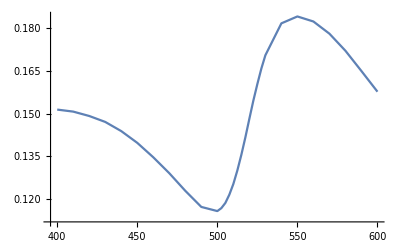

-Graphics-

```mathematica
data[[1,1]]//ListLinePlot
data[[1,3]]//ListLinePlot
```

```mathematica
data = FileNames["1*","Oblique*"]; data//TableForm

data =Drop[Import[#,"Data"],5]&/@ data;
cases = {2,3,5,6,8,9,11,12};

maxPoints =Map[Partition[#,2]&, Table[maxPair[data[[#1,10;;]],1+#2]&[i,j],{i,Length[data]},{j,cases}] ];
data = Map[Partition[#,2]&,makePairs[data,cases]] (*pol,angle,Sca/Abs,wlenth, Q*);
Dimensions[data]
```

Oblique-Supported-Internal/1-Efficiency-p.csv
Oblique-Supported-Internal/1-Efficiency-s.csv

{2,4,2,30,2}

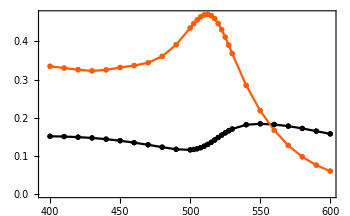
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListPlot[#1,ImageSize->350,PlotRange->All,Evaluate[graphsOpts],Joined->True]&/@ data[[1]]
```

```mathematica
MapThread[Show[{
ListPlot[#1,ImageSize->350,PlotRange->All,Evaluate[graphsOpts],Joined->True, AspectRatio->1],
ListPlot[Callout[#,ToString[NumberForm[N[#[[1]]],{4,1}]],Below]&/@#,PlotStyle->Blue]& @ #2}]&,{data,maxPoints},2]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

Near Field Abs

```mathematica
data =  FileNames["2*","Normal"]
data//TableForm
data =Drop[Import[#,"Data"],8]&/@ data;
lim = radius*4;
```

{Normal/2-Abs-Near-Embedded-External.csv,Normal/2-Abs-Near-Embedded-Internal.csv,Normal/2-Abs-Near-Supported-External.csv,Normal/2-Abs-Near-Supported-Internal.csv}

Normal/2-Abs-Near-Embedded-External.csv
Normal/2-Abs-Near-Embedded-Internal.csv
Normal/2-Abs-Near-Supported-External.csv
Normal/2-Abs-Near-Supported-Internal.csv

```mathematica
max = Max[data[[;;,;;,4]]] (*To normalize all cases*)
case = {1,-1,1,-1} (*To place above or below the glass*)

dataX = Table[Select[data[[i]], Abs[#[[2]]]<.001   &],{i,Length[data]}];
dataX = MapThread[#1/. {x_,y_,z_,norm_} -> {x, #2 * z, norm/max} &,{dataX, case}];
dataX = Table[Select[dataX[[i]], (Abs[#[[1]]]<lim && Abs[#[[2]]]<lim) &],{i,Length[dataX]}];

dataY = Table[Select[data[[i]], Abs[#[[1]]]<.001   &],{i,Length[data]}];
dataY = MapThread[#/. {x_,y_,z_,norm_} -> {y, #2 * z, norm/max} &, {dataY, case}];
dataY = Table[Select[dataY[[i]], (Abs[#[[1]]]<lim && Abs[#[[2]]]<lim) &],{i,Length[dataY]}];
```

5.55566

{1,-1,1,-1}

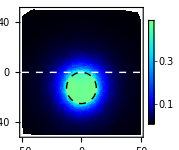
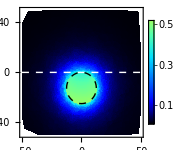
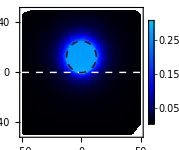
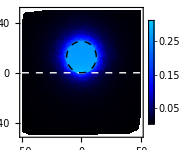

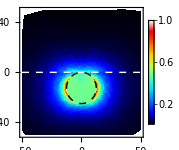
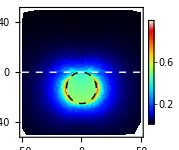
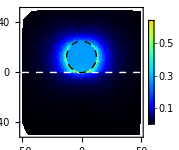
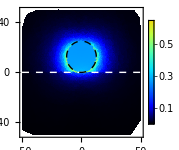

```mathematica
system = {White,Dashed, Line[{{-lim,0},{lim,0}}],Black, Circle[{0,radius*#},radius]}&/@{-1,-1,1,1};

plotsX = MapThread[ListDensityPlot[#1,ColorFunctionScaling->False,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataX,system}]
plotsY = MapThread[ListDensityPlot[#1,ColorFunctionScaling->False,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataY,system}]
```

Near Field Sca

```mathematica
data =  FileNames["3*","Normal"]
data//TableForm
data =Drop[Import[#,"Data"],8]&/@ data;
lim = radius*4;
```

{Normal/3-Sca-Near-Embedded-External.csv,Normal/3-Sca-Near-Embedded-Internal.csv,Normal/3-Sca-Near-Supported-External.csv,Normal/3-Sca-Near-Supported-Internal.csv}

Normal/3-Sca-Near-Embedded-External.csv
Normal/3-Sca-Near-Embedded-Internal.csv
Normal/3-Sca-Near-Supported-External.csv
Normal/3-Sca-Near-Supported-Internal.csv

```mathematica
max = Max[data[[;;,;;,4]]] (*To normalize all cases*)
case = {1,-1,1,-1} (*To place above or below the glass*)

dataX = Table[Select[data[[i]], Abs[#[[2]]]<.001   &],{i,Length[data]}];
dataX = MapThread[#1/. {x_,y_,z_,norm_} -> {x, #2 * z, norm/max} &,{dataX, case}];
dataX = Table[Select[dataX[[i]], (Abs[#[[1]]]<lim && Abs[#[[2]]]<lim) &],{i,Length[dataX]}];

dataY = Table[Select[data[[i]], Abs[#[[1]]]<.001   &],{i,Length[data]}];
dataY = MapThread[#/. {x_,y_,z_,norm_} -> {y, #2 * z, norm/max} &, {dataY, case}];
dataY = Table[Select[dataY[[i]], (Abs[#[[1]]]<lim && Abs[#[[2]]]<lim) &],{i,Length[dataY]}];
```

5.90529

{1,-1,1,-1}

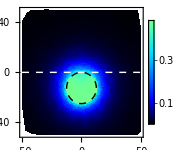
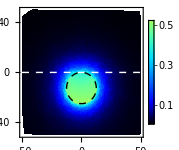
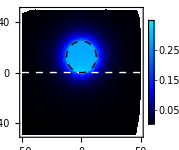
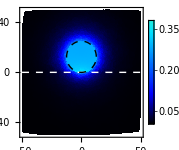

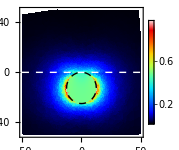
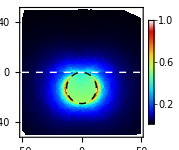
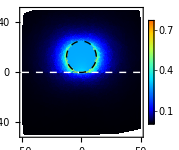
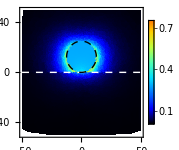

```mathematica
system = {White,Dashed, Line[{{-lim,0},{lim,0}}],Black, Circle[{0,radius*#},radius]}&/@{-1,-1,1,1};

plotsX = MapThread[ListDensityPlot[#1,ColorFunctionScaling->False,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataX,system}]
plotsY = MapThread[ListDensityPlot[#1,ColorFunctionScaling->False,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataY,system}]
```

Far Field (Normal X, All WaveLengths)

```mathematica
data =  FileNames["4*","Normal"]; data//TableForm
data =Drop[Import[#,"Data"],8]&/@ data;
data = Map[Partition[#,51]&,data]; (*Separete eat wlength value*)
data = Map[Table[#[[i]],{i,1,30,4}]&,data]; (*Choose some wlength*)
```

Normal/4-Far-NormalX-Embedded-External.csv
Normal/4-Far-NormalX-Embedded-Internal.csv
Normal/4-Far-NormalX-Supported-External.csv
Normal/4-Far-NormalX-Supported-Internal.csv

```mathematica
thTiks=Table[{i*Pi/180.,
Which[i≤90,(90-i)Degree,
i<= 180,""(*Mod[i,90]*),
i< 270,(90-Mod[i,90])Degree,
True, Mod[i,90]Degree
]},{i,0,360,15}];

arrows ={Red,Arrow[-#2*{{Cos[#1],Sin[#1]},.025{Cos[#1],Sin[#1]}}]}&;
```

```mathematica
max = Max[#[[;;,;;,2]]]&/@data;
caseNP = {-1,-1,1,1}; (*To place above or below the glass*)
caseDir = {-1,1,-1,1}; (*To place the incoming wave direction*)

MapThread[
ListPolarPlot[#1/.{theta_,rad_}-> {theta+Pi/2.,rad},PlotRange->#2*1.65,
PolarAxesOrigin->{{Left,Up},#2},
Evaluate[graphsOptsPolar],
PolarTicks->{thTiks[[;;-2]],Automatic},
Prolog->{LightBlue,Disk[{0,0},#2*1.65,{0,-Pi}],LightYellow,Disk[#3*{0,#2}/3.5,#2/3.5]},
Epilog->arrows[Pi/2,#4*#2*1.1]
]&,
{data,max,caseNP,caseDir}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Far Field (Normal Y, All WaveLengths)

```mathematica
data =  FileNames["5*","Normal"]; data//TableForm
data =Drop[Import[#,"Data"],8]&/@ data;
data = Map[Partition[#,51]&,data]; (*Separete eat wlength value*)
data = Map[Table[#[[i]],{i,1,30,4}]&,data]; (*Choose some wlength*)
```

Normal/5-Far-NormalY-Embedded-External.csv
Normal/5-Far-NormalY-Embedded-Internal.csv
Normal/5-Far-NormalY-Supported-External.csv
Normal/5-Far-NormalY-Supported-Internal.csv

```mathematica
thTiks=Table[{i*Pi/180.,
Which[i≤90,(90-i)Degree,
i<= 180,""(*Mod[i,90]*),
i< 270,(90-Mod[i,90])Degree,
True, Mod[i,90]Degree
]},{i,0,360,15}];

arrows ={Red,Arrow[-#2*{{Cos[#1],Sin[#1]},.025{Cos[#1],Sin[#1]}}]}&;
```

```mathematica
max = Max[#[[;;,;;,2]]]&/@data;
caseNP = {-1,-1,1,1}; (*To place above or below the glass*)
caseDir = {-1,1,-1,1}; (*To place the incoming wave direction*)

MapThread[
ListPolarPlot[#1/.{theta_,rad_}-> {theta+Pi/2.,rad},PlotRange->#2*1.65,
PolarAxesOrigin->{{Left,Up},#2},
Evaluate[graphsOptsPolar],
PolarTicks->{thTiks[[;;-2]],Automatic},
Prolog->{LightBlue,Disk[{0,0},#2*1.65,{0,-Pi}],LightYellow,Disk[#3*{0,#2}/3.5,#2/3.5]},
Epilog->arrows[Pi/2,#4*#2*1.1]
]&,
{data,max,caseNP,caseDir}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}